```mathematica
boat = ImplicitRegion[x^2/2<y<2 && -2 < x<2&&0<y<2 && -5 < z <5, {x,y,z}];
mass = NIntegrate[300, {x,y, z}∈boat]+5000;
com = N[ 1/mass*Integrate[300*{x,y,z}, {x,y,z}∈boat]];
fgrav = -(mass * 9.8);
fbuoy = -fgrav;
maxdisp = disp/.{d->2};
displaced = N[fgrav/(1000*9.8)];
Momentarm[theta_]:=(
(* Returns the moment of the boat
theta_: the heel angle in degrees *)
rads = theta * (Pi/180);
water = ImplicitRegion[y<Tan[rads]*x+d&&-2<x<2&&0<y<2 && -5<z<5,{x,y, z}];
under = RegionIntersection[boat,water];
disp = Integrate[1000, {x,y,z}∈under];
waterline =Quiet[NSolve[disp==mass,d,Reals]];
draft = N[d /. waterline[[1]]];
cob = RegionCentroid[under/.{d->draft}];
moment = Piecewise[{
{(cob-com)×(fbuoy*{-Sin[rads],Cos[rads],0}) , rads < Pi/2},
{(-(cob-com)×(fbuoy*{-Sin[-rads],Cos[-rads],0})), rads > Pi/2}
}][[3]]
)
```

```mathematica
Momentarm[30]
```

91518.2

```mathematica
(*NIntegrate[300, {x,y,z}∈ImplicitRegion[x^4/2<y<2 && -2 < x<2&&0<y<2 && -5 < z <5, {x,y, z}]]*)
```

13576.5

```mathematica
curve = Quiet[Parallelize[Table[{angle, Momentarm[angle]},{angle,0,179, 5}]]];
```

ImplicitRegion::msgs: 
   Evaluation of {Notebook$$15$997754`y < 
       Tan[Notebook$$15$997754`rads] Notebook$$15$997754`x + 
        Notebook$$15$997754`d && -2 < Notebook$$15$997754`x < 2 && <<1>> && 
      -5 < Notebook$$15$997754`z < 5, True} generated message(s) {Less::nord}.

ImplicitRegion::msgs: 
   Evaluation of {Notebook$$15$997754`y < ComplexInfinity && 
      -2 < Notebook$$15$997754`x < 2 && 0 < Notebook$$15$997754`y < 2 && 
      -5 < Notebook$$15$997754`z < 5, True} generated message(s) {Less::nord}.

Less::nord: Invalid comparison with ComplexInfinity attempted.

Part::partw: Part 1 of {} does not exist.

ReplaceAll::reps: 
   {{}[[1]]} is neither a list of replacement rules nor a valid dispatch
     table, and so cannot be used for replacing.

RegionCentroid::nmet: 
   Unable to compute the centroid of region 
    ImplicitRegion[Notebook$$15$997754`y < ComplexInfinity && 
      -5 < Notebook$$15$997754`z < 5 && -2 < Note<<15>>`x < 2 && <<1>> && 
                           2
      Notebook$$15$997754`x
      ---------------------- < Notebook$$15$997754`y < 2, {<<3>>}].
                2

Part::partd: Part specification 0[[3]] is longer than depth of object.

Part::partd: Part specification 0.⟦3⟧ is longer than depth of object.

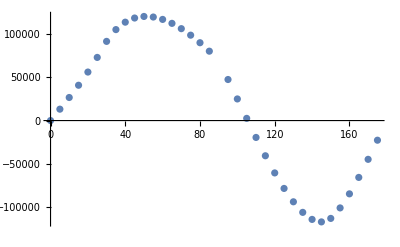

Part::partd: Part specification 0.⟦3⟧ is longer than depth of object.

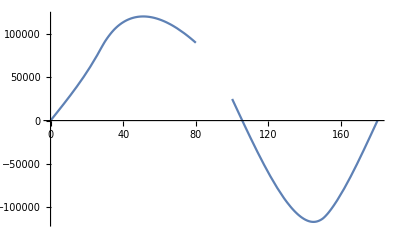

{x→105.567}

```mathematica
ListPlot[curve, AxesLabel->Automatic]
f=Interpolation[curve];
Plot[f[x],{x,0,180}]
FindRoot[f[x]==0, {x,100}]
```